### Simplex Plot

```mathematica
(* Geometric transformation to simplex *)
{err,trans}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
(* Edges of simplex *)
triangle=Graphics[{Thickness[0.005],Darker[Gray],GeometricTransformation[Line[{{0,0},{0,1},{1,0},{0,0}}],trans]}];
(* Some random data *)
dummyData=Select[RandomReal[1,{100,2}],Total[#]<=1&];
(* Plot the points *)
points=ListPlot[dummyData,PlotStyle->PointSize[0.03]];
(* Or plot the lines *)
lines=ListLinePlot[dummyData,PlotStyle->Black];
(* Show all together *)
(* The trick is to extract the "First" part of the plots, and transform it *)
```

## Data processing

```mathematica
SetDirectory[NotebookDirectory[]<>"simulation_data/"]
```

/Users/chaitanyagokhale/Documents/Working/Srishti/matecopying_multiplemorphs/fig3_new/simulation_data

```mathematica
filenames=FileNames[];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/chaitanyagokhale/Documents/Working/Srishti/matecopying_multiplemorphs/fig3_new

```mathematica
filenames
```

{21}

```mathematica
raw3mdata=Table[Import[NotebookDirectory[]<>"simulation_data/"<>ToString[filenames⟦i⟧],"CSV"],{i,1,Length[filenames],1}];
```

```mathematica
raw3mdata//Dimensions
```

{21,1275,4}

```mathematica
raw3mdata⟦1⟧⟦1;;10⟧
```

{{h,l,h_eq,l_eq},{0.,1.,0.,1.},{0.,0.979592,0.,0.62},{0.,0.959184,0.,0.48},{0.,0.938776,0.,0.3},{0.,0.918367,0.,0.2},{0.,0.897959,0.,0.22},{0.,0.877551,0.,0.12},{0.,0.857143,0.,0.06},{0.,0.836735,0.,0.02}}

```mathematica
cols=ColorData[97,"ColorList"]⟦{2,1,3}⟧
```

{RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.560181, 0.691569, 0.194885]}

0.

```mathematica
file1=.;
```

```mathematica
transformedlist=Table[Join[trans[{#⟦2⟧,1-#⟦2⟧-#⟦1⟧}],{#⟦3⟧}]&/@raw3mdata⟦i,2;;⟧,{i,1,Length[filenames],1}];
```

```mathematica
plots=Table[Show[triangle,ListDensityPlot[transformedlist⟦i⟧,InterpolationOrder->2,ColorFunction->"SandyTerrain",PlotLegends->Automatic,PlotLayout->{"Row", 2},Frame->False,PlotRange->All,Epilog->Inset[Graphics[Text[ToString[filenames⟦i⟧]]],{0.2,0.7}]]],{i,1,20,1}];
```

```mathematica
ListAnimate[plots]
```

```mathematica
Export[NotebookDirectory[]<>"cdynamics.mov",plots]
```

/Users/chaitanyagokhale/Documents/Working/Srishti/Overleafdata/matecopying_multiplemorphs/fig3_new/cdynamics.mov

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

```mathematica
coltab=Show[triangle,ListDensityPlot[transformedlist⟦20⟧,InterpolationOrder->2,ColorFunction->#,PlotLegends->Automatic,PlotLayout->{"Row", 2},Frame->False,PlotRange->All,Epilog->Inset[Graphics[Text[ToString[#]]],{0.2,0.7}]]]&/@ColorData["Gradients"];
```

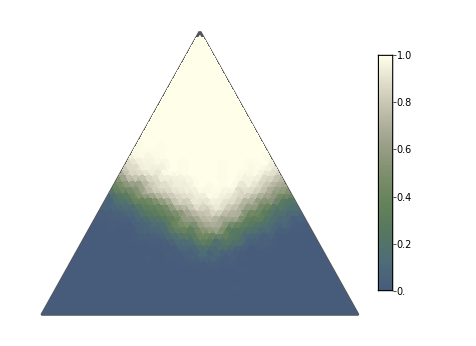
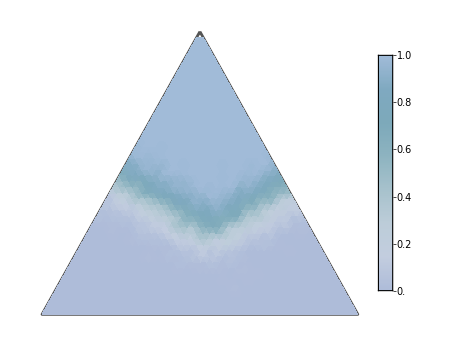
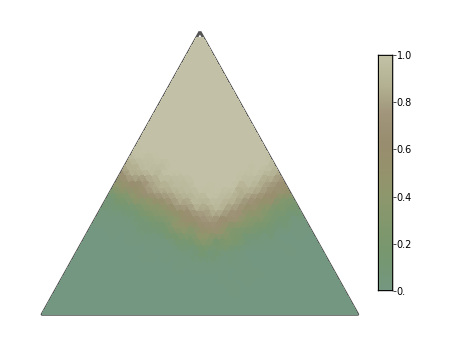
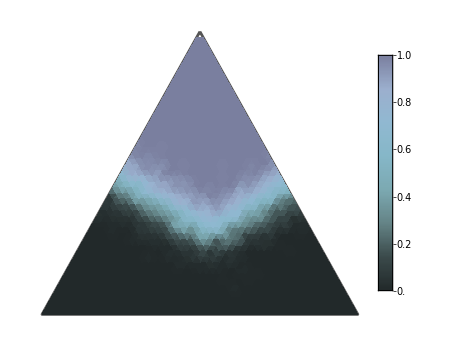
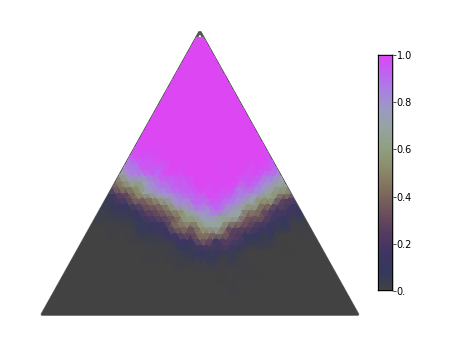
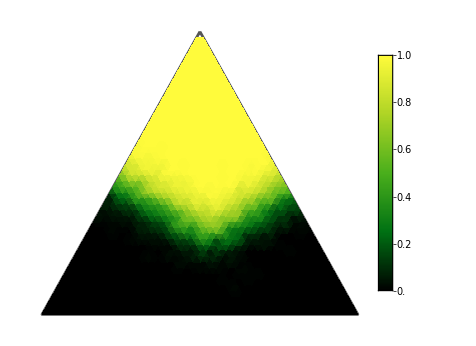
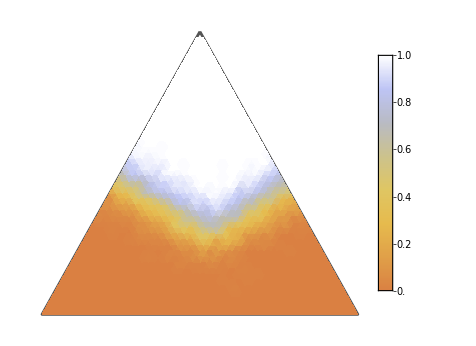
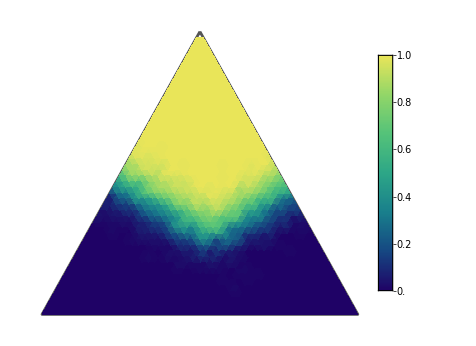

```mathematica
coltab
```

## Using two variables

```mathematica
datatransformedlist=Table[Style[trans[{#⟦2⟧,1-#⟦2⟧-#⟦1⟧}],Blend[cols,{#⟦4⟧,1-#⟦3⟧-#⟦4⟧,#⟦3⟧}]]&/@raw3mdata⟦i,2;;⟧,{i,1,Length[filenames],1}];
```

```mathematica
cols
```

{RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.560181, 0.691569, 0.194885]}

```mathematica
datatransformedlist⟦1⟧
```

```mathematica
plots=Table[Show[ListDensityPlot[transformedlist⟦i⟧,InterpolationOrder->2,ColorFunction->"LightTemperatureMap",PlotLegends->Automatic,PlotLayout->{"Row", 2},Frame->False,PlotRange->All,Epilog->Inset[Graphics[Text[ToString[filenames⟦i⟧]]],{0.2,0.7}]],triangle],{i,1,Length[filenames],1}];
```

```mathematica
dataplots=Table[Show[triangle,ListPlot[datatransformedlist⟦i⟧,InterpolationOrder->2,PlotStyle->PointSize[Medium],Axes->False,AspectRatio->1],inteqdyn],{i,1,Length[filenames],1}];
```

```mathematica
filenames⟦21⟧
```

3m_c1.00.csv

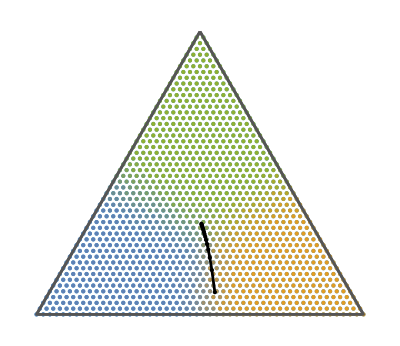

```mathematica
dataplots⟦21⟧
```

```mathematica
ListAnimate[dataplots]
```

```mathematica
α=0.8;β=2;γ=.;u=0;
q1=2;q2=2.1;q3=2.3;
p[γ_,y_,q_]:=(1-γ)q/(q1+q2+q3)+α γ (y^β/(y^β+(1-y)^β));
```

```mathematica
internal={};
For[γ=0,γ<=1.0,γ=γ+0.05,
dy1[y1_,y2_]:=y1(u ((q1^2-(y1 q1^2+y2 q2^2+(1-y1-y2) q3^2))/(q1+q2+q3))+(1-u)(p[γ,y1,q1] q1-(p[γ,y1,q1] q1 y1+p[γ,y2,q2] q2 y2+p[γ,(1-y1-y2),q3] q3 (1-y1-y2))));
dy2[y1_,y2_]:=y2 (u ((q2^2-(y1 q1^2+y2 q2^2+(1-y1-y2) q3^2))/(q1+q2+q3))+(1-u)(p[γ,y2,q2] q2-(p[γ,y1,q1] q1 y1+p[γ,y2,q2] q2 y2+p[γ,(1-y1-y2),q3] q3 (1-y1-y2))));
y1=.;
y2=.;
sol=NSolve[{dy1[y1,y2]==0,dy2[y1,y2]==0},{y1,y2},Reals];
data={y1,y2}/.sol;
relData=Select[data,#⟦1⟧>0&&#⟦2⟧>0&&Total[#]<1.&&Total[#]>0&];
AppendTo[internal,{γ,If[relData=={},Missing[],trans[relData⟦1⟧]]}];
]
```

Part::partd: Part specification y1⟦1⟧ is longer than depth of object.

Part::partd: Part specification y1⟦2⟧ is longer than depth of object.

Part::partd: Part specification y2⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
internal⟦All,1⟧
```

{0,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

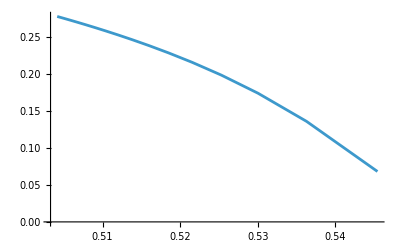

```mathematica
ListPlot[internal⟦All,2⟧,Joined->True]
```

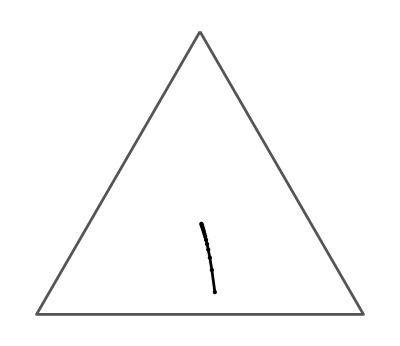

```mathematica
inteqdyn=Show[triangle,ListPlot[internal⟦All,2⟧,Joined->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.005]],Mesh->All,MeshStyle->Directive[PointSize[Medium],Black]]]
```